```mathematica
gammavalue
```

764.277

```mathematica
bsqvalue
```

4.1388×10^7

```mathematica
sigmaes
```

6.65077×10^-25

```mathematica
Nlayers
```

1

```mathematica
dtauradscads
```

1.7684×10^-15

```mathematica
Hradsca
```

2.18252×10^13

```mathematica
Frec
```

2.48156×10^18

```mathematica
frad0
```

1.24078×10^18

```mathematica
tauradabs
```

5.47031×10^-15

```mathematica
tauradtot
```

0.0385955

```mathematica
tauradsca
```

0.0385955

```mathematica
damptaurad
```

9.79154×10^-15

```mathematica
urad
```

7.40822×10^7

```mathematica
Prad
```

2.46941×10^7

```mathematica
damptaurad2
```

5.47031×10^-15

```mathematica
Frad
```

1.24078×10^18

```mathematica
taupairL
```

0

```mathematica
Lpnum
```

0

```mathematica
Lp
```

0

```mathematica
lmode
```

2

```mathematica
Rjet
```

1.09126×10^13

```mathematica
mmode
```

0

```mathematica
Lp
```

1.71415×10^13

```mathematica
Lpnum
```

1.71415×10^13

```mathematica
e1
```

0

```mathematica
e2
```

0

```mathematica
El1
```

1.19318×10^-16

```mathematica
solsT
```

FindRoot::precw: The precision of the argument function (2.4694054651680503`*^7 + 9.791541701785459`*^-15 (4.549956889287827`*^20 + Underflow[] b) + 1.4684306086381064`*^-6 T == 2.0693987877804406`*^7) is less than WorkingPrecision (20.).

FindRoot::nlnum: The function value {4.01475107996247811732804552757591932`18.946436248426217*^6 + 9.791541701785459098643974838616315`20.*^-15 (4.54995688928782712832`20.*^20 + Underflow[] b)} is not a list of numbers with dimensions {1} at {T} = {1.`20.*^10}.

FindRoot[Pg==Pm,{T,10^10},WorkingPrecision→20]

```mathematica
-(kb*T//.{T->10^9})/El1
```

-1.15712×10^9

```mathematica
god=N[Exp[-10^9.],15]
```

General::unfl: Underflow occurred in computation.

Underflow[]

```mathematica
If[god=!=Underflow[],god,0]
```

0

```mathematica
god=!=UnderFlow[]
```

True

```mathematica
Chop[Underflow[]]
```

0

```mathematica
Chop[15]
```

15

```mathematica
N[UnderFlow[]]
```

UnderFlow[]

```mathematica
e1=Exp[-me*c^2/(kb*T)]//.consts//.{T->10^9}
```

0.00265886

```mathematica
If[e1=!=Underflow[],e1,0]
```

0.00265886

```mathematica
e1=!=5
```

True

```mathematica
e1=!=UnderFlow[]
```

True

```mathematica
fuck=UnderFlow[]
```

UnderFlow[]

```mathematica
If[fuck=!=UnderFlow[]
```

```mathematica
e2
```

Overflow[]

```mathematica
e1
```

1.00103

```mathematica
solsT
```

{T→-5.7579677149311241559×10^12}

```mathematica
El1=( (me*c^2)^2+2*hbar*c*q*Sqrt[bsqvalue])^(1/2) - me*c^2
e2=Exp[-kb*T/(El1)]//.consts//.{T->10^9}
e2=If[e2=!=Underflow[],e2,0]
```

1.19318×10^-16

General::unfl: Underflow occurred in computation.

Underflow[]

0

```mathematica
Ug
```

2.20265×10^-6 T+3 ((2.52198×10^-15 (2 √3+3 (0.0385955/(1+0.0151346/T^2)+(5.47031×10^21)/T^4)) T^4)/(2 √3+3 (0.0385955/(1+0.0151346/T^2)+(5.47031×10^21)/T^4)+3.6561×10^-22 T^4)+((2 √3+3 (0.0385955/(1+0.0151346/T^2)+(5.47031×10^21)/T^4)) (354093. b ⅇ^(-(5.92986×10^9)/T-1.15712 T) √T+5.27186×10^9 ⅇ^(-5.92986×10^9/T) (1-ⅇ^(-1.15712 T)) T^(3/2)+2.54437×10^-10 b ⅇ^(-(5.92986×10^9)/T-1.15712 T) T^2+4.41346×10^-15 ⅇ^(-5.92986×10^9/T) (1-ⅇ^(-1.15712 T)) T^4))/(2 √3+3 (0.0385955/(1+0.0151346/T^2)+(5.47031×10^21)/T^4)+3.6561×10^-22 T^4))

```mathematica
Um
```

2.0694×10^7

```mathematica
Ug
```

2.20265×10^-6 T+3 ((2.52198×10^-15 (2 √3+3 (0.0385955/(1+0.0151346/T^2)+(5.47031×10^21)/T^4)) T^4)/(2 √3+3 (0.0385955/(1+0.0151346/T^2)+(5.47031×10^21)/T^4)+3.6561×10^-22 T^4)+((2 √3+3 (0.0385955/(1+0.0151346/T^2)+(5.47031×10^21)/T^4)) (354093. b ⅇ^(-(5.92986×10^9)/T-1.15712 T) √T+5.27186×10^9 ⅇ^(-5.92986×10^9/T) (1-ⅇ^(-1.15712 T)) T^(3/2)+2.54437×10^-10 b ⅇ^(-(5.92986×10^9)/T-1.15712 T) T^2+4.41346×10^-15 ⅇ^(-5.92986×10^9/T) (1-ⅇ^(-1.15712 T)) T^4))/(2 √3+3 (0.0385955/(1+0.0151346/T^2)+(5.47031×10^21)/T^4)+3.6561×10^-22 T^4))

```mathematica
Pe//.{T->10^10}
```

7342.15

```mathematica
El1//.{T->10^9}
```

1.19318×10^-16

```mathematica
kb*T/(El1)//.{T->10^9}
```

1.15712×10^9

```mathematica
e2=Exp[-Min[kb*T/(El1),10^4.]]
```

ⅇ^(-Min[10000.,1.15712 T])

```mathematica
e2//.{T->10^9.}
```

1.1354838653×10^-4343

```mathematica
e2
```

ⅇ^(-Min[10000.,1.15712 T])

```mathematica
solsT
```

{T→1.×10^10}

```mathematica
Pm
```

2.0694×10^7

```mathematica
Pm
```

2.0694×10^7

```mathematica
10^5.3
```

199526.

```mathematica
Ug//.{T->10^5.3}
Um
```

1.15125×10^7

2.0694×10^7

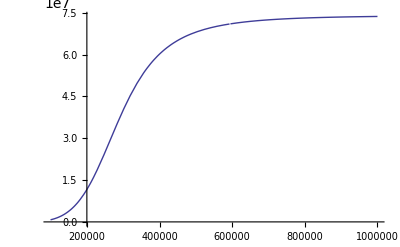

```mathematica
Plot[Ug,{T,10^5,10^6}]
```

```mathematica
omegape
```

1.68978×10^11

```mathematica
T0=10^6;solsT0=FindRoot[Ug==Um,{T,T0},WorkingPrecision->20];If[solsT0[[1]]≠T0 && solsT0[[1]]>0.0,solsT=solsT0];
```

FindRoot::precw: The precision of the argument function (2.2026459129571595`*^-6 T + 3 (2.521978193401108`*^-15 (2 Power[« 2 »] + 3 Plus[« 2 »]) T^4/Times[« 2 »] + Times[« 2 »] + Times[« 2 »] + (2 Power[« 2 »] + 3 Plus[« 2 »]) (« 1 »)/Times[« 2 »] + Times[« 2 »] + Times[« 2 »]) == 2.0693987877804406`*^7) is less than WorkingPrecision (20.).

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {T} = {-1.`20.}.

```mathematica
solsT0[[1,2]]==10^5
```

False

```mathematica
T0=10^4;solsT0=FindRoot[Ug==Um,{T,T0},WorkingPrecision->20];If[solsT0[[1,2]]≠T0 && solsT0[[1,2]]>0.0,solsT=solsT0];
T0=10^5;solsT0=FindRoot[Ug==Um,{T,T0},WorkingPrecision->20];If[solsT0[[1,2]]≠T0 && solsT0[[1,2]]>0.0,solsT=solsT0];
T0=10^6;solsT0=FindRoot[Ug==Um,{T,T0},WorkingPrecision->20];If[solsT0[[1,2]]≠T0 && solsT0[[1,2]]>0.0,solsT=solsT0];
T0=10^7;solsT0=FindRoot[Ug==Um,{T,T0},WorkingPrecision->20];If[solsT0[[1,2]]≠T0 && solsT0[[1,2]]>0.0,solsT=solsT0];
T0=10^8;solsT0=FindRoot[Ug==Um,{T,T0},WorkingPrecision->20];If[solsT0[[1,2]]≠T0 && solsT0[[1,2]]>0.0,solsT=solsT0];
T0=10^9;solsT0=FindRoot[Ug==Um,{T,T0},WorkingPrecision->20];If[solsT0[[1,2]]≠T0 && solsT0[[1,2]]>0.0,solsT=solsT0];
T0=10^10;solsT0=FindRoot[Ug==Um,{T,T0},WorkingPrecision->20];If[solsT0[[1,2]]≠T0 && solsT0[[1,2]]>0.0,solsT=solsT0];
T0=10^11;solsT0=FindRoot[Ug==Um,{T,T0},WorkingPrecision->20];If[solsT0[[1]]≠T0 && solsT0[[1]]>0.0,solsT=solsT0];
```

FindRoot::precw: The precision of the argument function (2.2026459129571595`*^-6 T + 3 (2.521978193401108`*^-15 (2 Power[« 2 »] + 3 Plus[« 2 »]) T^4/Times[« 2 »] + Times[« 2 »] + Times[« 2 »] + (2 Power[« 2 »] + 3 Plus[« 2 »]) (« 1 »)/Times[« 2 »] + Times[« 2 »] + Times[« 2 »]) == 2.0693987877804406`*^7) is less than WorkingPrecision (20.).

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {T} = {-1.`20.}.

FindRoot::precw: The precision of the argument function (2.2026459129571595`*^-6 T + 3 (2.521978193401108`*^-15 (2 Power[« 2 »] + 3 Plus[« 2 »]) T^4/Times[« 2 »] + Times[« 2 »] + Times[« 2 »] + (2 Power[« 2 »] + 3 Plus[« 2 »]) (« 1 »)/Times[« 2 »] + Times[« 2 »] + Times[« 2 »]) == 2.0693987877804406`*^7) is less than WorkingPrecision (20.).

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {T} = {-1.`20.}.

FindRoot::precw: The precision of the argument function (2.2026459129571595`*^-6 T + 3 (2.521978193401108`*^-15 (2 Power[« 2 »] + 3 Plus[« 2 »]) T^4/Times[« 2 »] + Times[« 2 »] + Times[« 2 »] + (2 Power[« 2 »] + 3 Plus[« 2 »]) (« 1 »)/Times[« 2 »] + Times[« 2 »] + Times[« 2 »]) == 2.0693987877804406`*^7) is less than WorkingPrecision (20.).

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {T} = {-9.0000001`20.*^8}.

FindRoot::precw: The precision of the argument function (2.2026459129571595`*^-6 T + 3 (2.521978193401108`*^-15 (2 Power[« 2 »] + 3 Plus[« 2 »]) T^4/Times[« 2 »] + Times[« 2 »] + Times[« 2 »] + (2 Power[« 2 »] + 3 Plus[« 2 »]) (« 1 »)/Times[« 2 »] + Times[« 2 »] + Times[« 2 »]) == 2.0693987877804406`*^7) is less than WorkingPrecision (20.).

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

FindRoot::precw: The precision of the argument function (2.2026459129571595`*^-6 T + 3 (2.521978193401108`*^-15 (2 Power[« 2 »] + 3 Plus[« 2 »]) T^4/Times[« 2 »] + Times[« 2 »] + Times[« 2 »] + (2 Power[« 2 »] + 3 Plus[« 2 »]) (« 1 »)/Times[« 2 »] + Times[« 2 »] + Times[« 2 »]) == 2.0693987877804406`*^7) is less than WorkingPrecision (20.).

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {T} = {-4.1022330360901790952`20.*^10}.

FindRoot::precw: The precision of the argument function (2.2026459129571595`*^-6 T + 3 (2.521978193401108`*^-15 (2 Power[« 2 »] + 3 Plus[« 2 »]) T^4/Times[« 2 »] + Times[« 2 »] + Times[« 2 »] + (2 Power[« 2 »] + 3 Plus[« 2 »]) (« 1 »)/Times[« 2 »] + Times[« 2 »] + Times[« 2 »]) == 2.0693987877804406`*^7) is less than WorkingPrecision (20.).

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {T} = {-9.0000000001`20.*^11}.

```mathematica
solsT
```

{T→235600.69118008085215}

```mathematica
solsT
```

{T→1.×10^6}

```mathematica
Pg
```

2.91492×10^7+1.46843×10^-6 T

```mathematica
Pm
```

2.0694×10^7

```mathematica
Prad
```

(2.52198×10^-15 (2 √3+3 (5.47031×10^-15+0.0385955/(1+0.0151346/T^2))) T^4)/(3.6561×10^14+3 (5.47031×10^-15+0.0385955/(1+0.0151346/T^2)))

```mathematica
gettemperature
```

FindRoot::precw: The precision of the argument function (2.2026459129571595`*^-6 T + 3 (2.521978193401108`*^-15 (2 Power[« 2 »] + 3 Plus[« 2 »]) T^4/Times[« 2 »] + Times[« 2 »] + Times[« 2 »] + (2 Power[« 2 »] + 3 Plus[« 2 »]) (« 1 »)/Times[« 2 »] + Times[« 2 »] + Times[« 2 »]) == 2.0693987877804406`*^7) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {T} = {-1.`20.}.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General will be suppressed during this calculation.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {T} = {-1.`20.}.

FindRoot::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {T} = {-9.0000001`20.*^8}.

General::stop: Further output of FindRoot will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

```mathematica
solsT
```

{T→235600.69118008085215}

```mathematica
getDelta
```

```mathematica
vamix=c*Sqrt[bsqvalue/(rhobvalue*c^2+bsqvalue+Ug+Pg)]//.solsT[[1]]
```

2.19912×10^10

```mathematica
vaout=c*Sqrt[bsqvalue/(rhobvalue*c^2+bsqvalue)]//.solsT[[1]]
```

2.74617×10^10

```mathematica
muth=(me*c^2)/(kb*T)//.consts//.solsT[[1]]
```

25169.1

```mathematica
muth=50
```

50

```mathematica
Clear[muth]
```

```mathematica
omegaprelfactor=1.0*Sqrt[MeijerG[{{0},{2}},{{-1/2,1,3/2},{0}},muth^2/4]/(2*BesselK[2,muth])]
```

0.707107 √(MeijerG[{{},{2}},{{-1/2,1,3/2},{}},muth^2/4]/BesselK[2,muth])

```mathematica
omegaprelfactor//.{muth->19}
```

1.59744

```mathematica
MeijerG[{{0},{2}},{{-1/2,1,3/2},{0}},muth^2/4]//.{muth->15.}
MeijerG[{{0},{2}},{{-1/2,1,3/2},{0}},muth^2/4]//.{muth->19.}
```

1.91707×10^-7

9.05146×10^-9

```mathematica
2*BesselK[2,muth]//.{muth->15.}
2*BesselK[2,muth]//.{muth->19.}
```

2.23435×10^-7

3.54708×10^-9

```mathematica
Plot[omegaprelfactor,{muth,10,20}]
```

$Aborted

```mathematica
FullSimplify[Sqrt[MeijerG[{{0},{2}},{{-1/2,1,3/2},{0}},muth^2/4]/(2*BesselK[2,muth])],{muth≥0}]
```

(√(MeijerG[{{},{2}},{{-1/2,1,3/2},{}},muth^2/4]/BesselK[2,muth]))/(√2)

```mathematica
vamix
```

2.19912×10^10

```mathematica
vaout
```

2.74617×10^10

```mathematica
muth
```

25169.1

```mathematica
omegape
```

3.33926×10^11

```mathematica
muthp
```

muthp

```mathematica
muth=25169.1
```

25169.1

```mathematica
omegaprelfactor[muth]
```

0.99995

```mathematica
solT
```

solT

```mathematica
solsT
```

{T→235600.69118008085215}

```mathematica
conditionpt
```

8127.98

```mathematica
Um
```

2.0694×10^7

```mathematica
Ug//.{T->9.395*10^(12)}
```

2.06939×10^7

```mathematica
vrecsp
```

0.000156493

```mathematica
Lp
Pi*Rjet/2
```

1.71415×10^13

1.71415×10^13

```mathematica
mmode*omegafvalue/(gammavalue*2*Pi*c)
```

0

```mathematica
Lp
Pi*Rjet/2
```

8.50445×10^9

1.71415×10^13

```mathematica
vrecsp
```

0.00702578

```mathematica
etatotal
Deltaspt
```

0.0000152865

0.00217577

```mathematica
conditionpt
```

364908.

```mathematica
vrecsp
etatotal
Deltaspt
conditionpt
```

0.00135813

0.0000113135

0.00833019

951.484

```mathematica
Prad//.solsT[[1]]
Ppairs//.solsT[[1]]
Pbaryon//.solsT[[1]]
Pe//.solsT[[1]]
```

0.100276

0.175396

1.05973×10^11

1.05973×10^11

```mathematica
e1//.solsT[[1]]
e2//.solsT[[1]]
```

0.999505

1.1354838653×10^-4343

```mathematica
urad0//.solsT[[1]]
```

1.55506×10^38

```mathematica
damptaurad//.solsT[[1]]
```

1.9345×10^-39

```mathematica
tauradabs//.solsT[[1]]
tauradsca//.solsT[[1]]
```

3.70465×10^-40

2.32652

```mathematica
solsT
```

{T→1.1973504554244780788×10^13}

```mathematica
frad0/(c*urad0)//.solsT[[1]]
```

3.70465×10^-40

```mathematica
frfrac
```

9.46243×10^-13

```mathematica
vrecsp=c;
Frec=2*bsqvalue*vrecsp;
frad0=Frec;
tauradabs=frad0/(c*urad0)//.solsT[[1]]
```

8.17762×10^-27

```mathematica
u0=T^4
Q=T^(1/2)
Q/u0
```

T^4

√T

1/T^(7/2)

```mathematica
(me*c^2)^2/(q*(hbar*c)^3)
```

4.41638×10^46

```mathematica
(me^2*c^3/(q*hbar))
```

4.41428×10^13

```mathematica
sigmaff=T^(-1/2)*T^(-1)*B^(-2)
sigma0=sigmaff*(B/T)^2
```

1/(B^2 T^(3/2))

1/T^(7/2)

```mathematica
w=T
j=q^2/(hbar*c)*(me*c^2)^2/hbar*ne/(2*T^3)*T*Sqrt[2]/3*w
```

T

(1.0931×10^12 ne)/T

```mathematica
240/1.6
```

150.

```mathematica
urad=arad*T^4
Q0=1.6*10^(46)*(rho/10^(10))^2*(T/10^(11))^(1/2)
dtauds=Q0/(c*urad)
tau=dtauds*Rj
tau//.{h->0.02,r->10^(10),Rj->r*h,rho->10^10/10^4*(10^6/r)^1.5,T->10^6}
```

7.56593×10^-15 T^4

5.05964×10^20 rho^2 √T

(2.23068×10^24 rho^2)/T^(7/2)

(2.23068×10^24 rho^2 Rj)/T^(7/2)

1.47806×10^-13